```mathematica
$Assumptions=l>0
```

l>0

```mathematica
l1[θ_]:= (l √3)/Sin[(2π)/3-θ]
l2[θ_]:=l √(1-2 Sin[(2π)/3+θ]/Sin[(2π)/3-θ]+4(Sin[(2π)/3+θ]/Sin[(2π)/3-θ])^2)
```

```mathematica
f[θ_]:=l1[θ]+l2[θ]
```

```mathematica
FullSimplify[f[θ],Trig->True]
```

1/2 l (2 √3 Sec[π/6-θ]+√(Sec[π/6-θ]^2 (8+Cos[2 θ]-3 √3 Sin[2 θ])))

```mathematica
Minimize[{f[θ],0<=θ<=π/3},θ]
```

Minimize[{√3 l Sec[π/6-θ]+l √(1-2 Cos[π/6+θ] Sec[π/6-θ]+4 Cos[π/6+θ]^2 Sec[π/6-θ]^2),0≤θ≤π/3},θ]

```mathematica
Minimize[f[θ],θ]
```

Minimize[√3 l Sec[π/6-θ]+l √(1-2 Cos[π/6+θ] Sec[π/6-θ]+4 Cos[π/6+θ]^2 Sec[π/6-θ]^2),θ]

```mathematica
NMinimize[(f[θ]/.l->10),θ]
```

{-10.,{θ→-2.0944}}

```mathematica
NMinimize[{(f[θ]/.l->10),0<=θ<=π/3},θ]
```

{26.4575,{θ→0.713724}}

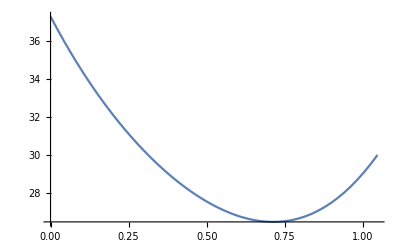

```mathematica
Plot[f[θ]/.l->10,{θ,0,π/3}]
```